# Dissipative interactions and decoherence

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
setFockSize[nmax_]:=Block[{},fockBasis =QuantumBasis[nmax];a=QuantumOperator[DiagonalMatrix[Table[Sqrt[i],{i,nmax-1}],1],nmax];
numberOp =a["Dagger"]@ a;
coherentTrunc =  QuantumState[Table[α^i/√(i!),{i,0,nmax-1}],nmax,"Parameters"->α];
coh = coherentTrunc["Normalize"];]
```

## Single quantum systems and ensembles

## Quantum jump approach for individual realizations

### Algorithm for general quantum jump

Calculate the current probability ΔP of emission of a photon in a time interval δt according to ΔP = γ ⟨Ψ | a^†a|Ψ⟩ δt where |Ψ ⟩ is one member of the ensemble

Obtain a random number 0 ≤ r < 1, compare with ΔP to decide emission

Emit if r < ΔP (field loses one photon), the system jumps to renormalized form |Ψ ⟩ → |Ψ_emit⟩ → â |Ψ⟩ / ⟨Ψ|  (â)^†â |Ψ ⟩^(1/2)

No emission r > ΔP, the system evolves according to
|Ψ ⟩ → |Ψ_emit⟩ → e^(- ⅈ δt H_eff)|Ψ⟩ / [⟨ Ψ | e^(ⅈ δt H_eff^†)e^(-ⅈ δt H_eff)|Ψ⟩]^(1/2) 
                             = e^(- ⅈ δt H_eff)|Ψ⟩ / [⟨ Ψ | e^(-γ δt a^†a)|Ψ⟩]^(1/2)
                             ≈ (1 - (ⅈ / h) H δt - (γ/2)t a^†a)|Ψ⟩ / (1-ΔP)^(1/2)
where (Ĥ)_eff = Ĥ - ⅈ h (γ/2)(â)^†â is the effective non Hermitian Hamiltonian describing non unitary evolution where the second term represents decay of the cavity field.

Iterate the process to record a trajectory of conditional evolution of one member of the ensemble with jump events  t_(1,)t_2...

Average observables over a big number of trajectories to get average behavior or whole ensemble

### Master equation for density operators

The history of a particular trajectory splits into two alternatives in a time Δt to allow at most one jump, either it jumps or it does not.
|Ψ ⟩ →   |Ψ_emit⟩ with probability ΔP, 
	     |Ψ_(no emit)⟩ with probability 1 - ΔP

For a pure state |Ψ ⟩ ⟨ Ψ | the evolution can be described as a sum of two outcomes:
|Ψ ⟩ ⟨ Ψ | → ΔP | Ψ_emit⟩ ⟨ Ψ_emit| + (1 - ΔP)  | Ψ_(no emit)⟩ ⟨ Ψ_(no emit)|
 = γ δt â |Ψ ⟩ ⟨ Ψ | (â)^† + {1-(ⅈ/h)H δt -(γ/2)δt a^†a}|Ψ ⟩ ⟨ Ψ | (1+(ⅈ/h)H δt -(γ/2)δt a^†a)
 ≈ |Ψ ⟩ ⟨ Ψ |  - ⅈ/h δt [ Ĥ, |Ψ ⟩ ⟨ Ψ | ] + 
      γ/2 δt (2 â| Ψ ⟩ ⟨ Ψ | (â)^† - (â)^†â| Ψ ⟩ ⟨ Ψ |- | Ψ ⟩ ⟨ Ψ |(â)^†â)

Averaging  over all the members of the ensemble:
ρ̂(t +δt) = ρ̂(t) - ⅈ/h δt [Ĥ, ρ̂]+γ/2 δt(2 âρ (â)^† - (â)^†â ρ̂ - ρ̂(â)^†â)

Taking the limit as δt → 0 we get a differential equation

Referred as the master equation which can also be obtained from more complicated methods for the T = 0 K damping problem

### Quantum jumps on familiar states

Assuming no interaction (Ĥ = 0) so only the dissipation acts. If we have an initial cavity field in a coherent state |α⟩ the no jump-evolution results:
e^(- (γ/2) δt a^†a) |α⟩ /√⟨α|e^(-γ δt a^†a) |α⟩   = |α e^(-γ δt/2) ⟩

```mathematica
setFockSize[50]
```

```mathematica
Clear[γ,δt]
```

```mathematica
Hdisp = - ⅈ h (γ/2) numberOp;
```

```mathematica
Clear[jumpCoherent]
```

```mathematica
jumpCoherent =QuantumState[Exp[- ⅈ Hdisp /h δt]@ coh[αcoh]/ 
Sqrt[(coh[αcoh]["Dagger"]@ Exp[-γ δt numberOp]@ coh[αcoh])["Scalar"]],
"Parameters"->{α,γ,δt}];
```

```mathematica
evolvedCoh =QuantumState[coherentTrunc[α ⅇ^(-γ δt/2)],"Parameters"->{α,γ,δt}];
```

```mathematica
αcoh = RandomReal[{0,3}] Exp[ⅈ RandomReal[{0,2Pi}]]
```

-0.282106+0.180205 ⅈ

```mathematica
{rγ,rδt}= {RandomReal[{0,2}],0.1}
```

{1.95656,0.1}

```mathematica
jumpCoherent[αcoh,rγ,rδt];
```

```mathematica
evolvedCoh[αcoh,rγ,rδt]["Normalize"];
```

```mathematica
(%-%%)["StateVector"]//Chop //Normal
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The coherent state remains a coherent state after the evolution, however, the amplitude of the state has an exponential decay due to the dissipative interaction Hamiltonian

If we now consider the cavity field is prepared in a even cat state  |ψ_e⟩  = 𝒩_e (|α⟩ + |-α⟩) where 𝒩_e   is  a normalization constant

```mathematica
evenCat =QuantumState[coherentTrunc[α]+coherentTrunc[-α],"Parameters"->α]["Normalize"];
```

The annihilation operator converts an even cat state to odd cat state

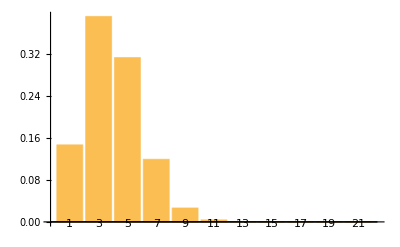

```mathematica
(a @ evenCat[2.])["ProbabilityPlot"]
```

For a no jump transition the field state decays referred as “jumping-cat” transition

exp(- γ δt (â)^†â/2) (|α⟩ ± |-α⟩) = ( |α e^(-γ δt/2)⟩ ± |-α e^(- γ δt /2)⟩ )

```mathematica
jumpCatState = QuantumState[Exp[-γ δt numberOp /2]@evenCat,"Parameters"->{α,γ,δt}];
```

```mathematica
jumpCatState[αcoh, rγ, rδt]["Normalize"];
```

```mathematica
evenCat[αcoh ⅇ^(-rγ rδt/2)];
```

```mathematica
(% - %%)["StateVector"]//Chop //Normal
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The cat state “reduce”  during no-jump evolution (the amplitude follows exponential decay)

## Decoherence

It can be defined as transformation over time of a quantum mechanical superposition into a classical statistical mixture, as a result of interaction with an environment. As an example, consider  an initial even cat state , the cavity-environment state is 
 |Ψ(0) ⟩ ∼ (|α⟩ + |-α⟩) | ϵ ⟩ 
 where |ϵ ⟩ is the quantum state of the environment. The environment can be described  with an arbitrary number of systems and states which are not relevant for the analysis. At a later time the system will evolve to 
 |Ψ(t) ⟩ ∼ (|β ⟩  | ϵ_1 ⟩ +| -β ⟩  | ϵ_2 ⟩ 
 with β = α e^(-γ t/ 2) from the earlier section so that the field becomes entangled with the environment. If we compute the density operator and trace over a complete set of states of the environment ⟨ϵ_i | ϵ_j⟩ = δ_ij, we get a reduced field density operator
  ρ_F(t) = Tr_Env ρ(t) = Σ ⟨ ϵ_i| ρ |ϵ_i ⟩ = |β(t)⟩⟨β(t)| + |-β(t)⟩⟨-β(t)| is a statistical mixture of two coherent states

### Decoherence of coherent state from master equation

Using the master equation for an initial coherent state |α⟩:

```mathematica
setFockSize[15]
αcoh = 2*Exp[I RandomReal[{0,2Pi}]];
```

```mathematica
ρ0 = coh[αcoh];
```

Establishing a damping parameter:

```mathematica
Clear[γ]
γ = RandomReal[{0,2}]
```

1.88587

Setting up the Liouvillian master equation with Ĥ=0 and L = â:

```mathematica
ℒ= QuantumOperator["Liouvillian"[0 * QuantumOperator[fockBasis],{a},{γ}]]
```

QuantumOperator[…]

```mathematica
expℒ=QuantumEvolve[I ℒ,None,{t,0,1}];
```

Verify the solution to the master equation is also a coherent state with complex amplitude α e^(- γ t /2) (fidelity remains around 1):

```mathematica
d=Table[QuantumDistance[coh[αcoh  Exp[-γ  t/2]],expℒ[t][ρ0]],{t,0,1,.01}];
```

```mathematica
d
```

{1.,0.999998,0.999997,0.999995,0.999994,0.999993,0.999993,0.999992,0.999992,0.999991,0.999991,0.999991,0.999991,0.999991,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.99999,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993}

The average number of photons follow an exponential decay

```mathematica
photons = Table[KeyValueMap[#1[[1]] #2&,expℒ[t][ρ0]["Probability"]]//Total,{t,0,1,0.01}] ;
```

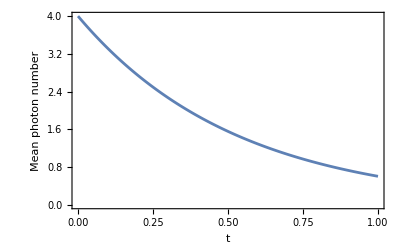

```mathematica
ListLinePlot[Thread[{Range[0,1,0.01],photons}],
Frame->True,
FrameLabel->(Style[#,14]&/@{"t","Mean photon number"})]
```

|α|^2exp(-γt) function represents what was obtained . The decay time of the field energy is T_decay= 1/γ

```mathematica
NonlinearModelFit[Thread[{Range[0,1,0.01],photons}],k Exp[-g t],{k,g},{t}]
```

FittedModel[…]

### Decoherence of an even cat state from master equation

Now we analyze the evolution of  a cavity prepared with an even cat state:

```mathematica
evenCat =QuantumState[coherentTrunc[α]+coherentTrunc[-α],"Parameters"->α]["Normalize"];
```

```mathematica
ρ0 = evenCat[αcoh];
```

```mathematica
Clear[γ]
γ = RandomReal[{0,2}]
```

1.73872

```mathematica
ℒ= QuantumOperator["Liouvillian"[0 * QuantumOperator[fockBasis],{a},{γ}]];
expℒ=QuantumEvolve[I ℒ,None,{t,0,1}];
```

Monitoring how the traces change. Tr[ρ^2] is related to the purity and also a measure of decoherence. But there will be a point that purity starts to increase because the decay in energy makes the state to start to get similar to the vacuum (pure state) :

```mathematica
traces = Table[{expℒ[t][ρ0]//Tr,expℒ[t][ρ0]["Purity"]},{t,0,1,0.01}];
```

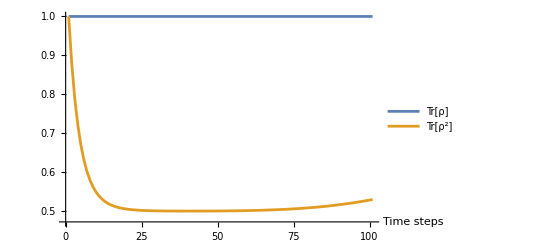

```mathematica
ListLinePlot[{traces[[All,1]],traces[[All,2]]},
PlotLegends->{"Tr[ρ]","Tr[ρ^2]"},
AxesLabel->{"Time steps",""}]
```

The energy decay (mean photon number) still decays exponentially as expected

```mathematica
photons = Table[KeyValueMap[#1[[1]] #2&,expℒ[t][ρ0]["Probability"]]//Total,{t,0,1,0.01}] ;
```

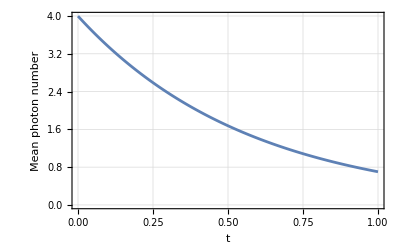

```mathematica
ListLinePlot[Thread[{Range[0,1,0.01],photons}],
Frame->True,
FrameLabel->(Style[#,14]&/@{"t","Mean photon number"}),
GridLines->Automatic,
FrameTicksStyle->13]
```

The theoretical solution of the master equation  is  ρ_F(t) = 𝒩_e^2[ | α ⅇ^(-γt/2)⟩ ⟨α ⅇ^(-γt/2)| + | -α ⅇ^(-γt/2)⟩ ⟨-α ⅇ^(-γt/2)| 
													+ ⅇ^(-2|α|^2(1-ⅇ^-γt))(| α ⅇ^(-γt/2)⟩ ⟨-α ⅇ^(-γt/2)| + | -α ⅇ^(-γt/2)⟩ ⟨α ⅇ^(-γt/2)| ) ]

```mathematica
sol =QuantumOperator[(coh[αcoh ⅇ^(-γ  t/2)]@coh[αcoh ⅇ^(-γ t /2)]["Dagger"]+ coh[-αcoh ⅇ^(-γ  t/2)]@coh[-αcoh ⅇ^(-γ  t/2)]["Dagger"])+ⅇ^(-2 Abs[αcoh]^2(1-ⅇ^(-γ t)))(coh[αcoh ⅇ^(-γ  t/2)]@coh[-αcoh ⅇ^(-γ t /2)]["Dagger"]+coh[-αcoh ⅇ^(-γ  t/2)]@coh[αcoh ⅇ^(-γ t /2)]["Dagger"]),"Parameters"->t]
```

```mathematica
AbsoluteTiming[distances = Table[QuantumDistance[expℒ[t][ρ0],sol[t]["MatrixQuantumState"]],{t,0,1,0.01}];]
```

{60.4261,Null}

Verifying are the same:

```mathematica
distances
```

{1.,1.,1.,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997}

Apart  from the energy decay we can see there is another quantity the decays from the theoretical solution ⅇ^(-2|α|^2(1-ⅇ^-γt)) multiply the “coherences”(off diagonal elements). For short times a decoherence time is obtained from expansion T_decoh = 1 / (2 γ |α|^2) = T_decay/(2(|α|)^2). T_decoh<T_decay as long as |α|^2  > 0.5

```mathematica
frames = Table[MatrixPlot[expℒ[t][ρ0]["DensityMatrix"]//Chop[#,10^-7]&,PlotLegends->Automatic,PlotLabel->StringTemplate["Magnitude of the elements of the density matrix \n T = `t`" ][<|"t"->t|>]],{t,0,1,0.02}];
```

```mathematica
ListAnimate[frames]
```

## Generation of coherent states from decoherence: optical balance

Dissipation destroy coherence in quantum superposition effects. However, even if it does not sound intuitive, it is also possible to create coherence from dissipative effects. The master equation has unitary(the commutator)and non-unitary terms(dissipation) with nonlinear behavior in the creation and annihilation operators. The interactions can “balance each other” such that the evolution at t → ∞  is  a different state than the vacuum.

Considering an interaction Hamiltonian OverHat[H_I] = h G(â+(â)^†)  where G is the strength of a classical pump field that propagates in a photon absorbing medium (dissipation). The master equation becomes:

We start with a random cavity field

```mathematica
ρ0 = QuantumState["RandomPure",fockBasis]
```

QuantumState[…]

```mathematica
G = RandomReal[{1,2}]
```

1.88637

Liouvillian of the master equation now we consider a driving interaction term  Ĥ ≠ 0

```mathematica
ℒ= QuantumOperator["Liouvillian"[G(a+a["Dagger"]),{a},{γ}]]
```

QuantumOperator[…]

The steady-state solution of the equation converges to ρ = |β ⟩ ⟨β| where β = - 2 ⅈ G/γ

```mathematica
expℒ=QuantumEvolve[I ℒ,None,{t,0,3}];
```

```mathematica
distances = Table[{t,QuantumDistance[expℒ[t][ρ0],coh[-I 2G/γ]]},{t,0,3,0.1}];
```

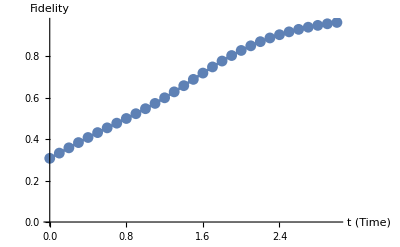

```mathematica
ListLinePlot[distances,Mesh->All,AxesLabel->{"t (Time)","Fidelity"}]
```

If we have an initial vacuum state  ρ̂(0) = |0⟩ ⟨0| at short times enough to ignore dissipation. The evolution will be unitary and we will get a coherent state  of the form
 | -ⅈ G t ⟩⟨- ⅈ G t | independent of γ . Fidelity remains around 1 for small times until the approximation is no longer valid

```mathematica
ρ0 = QuantumState["0",fockBasis];
```

```mathematica
distances = Table[{t,QuantumDistance[expℒ[t][ρ0],coh[-I G t]]},{t,0,0.8,0.02}];
```

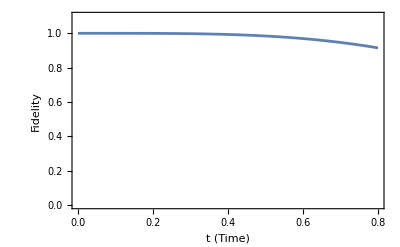

```mathematica
ListLinePlot[distances,PlotRange->{0,1.1},Frame->True,FrameLabel->{"t (Time)","Fidelity"}]
```